## Initializations

These two commands turn off the spell checker, 
otherwise we get spurious messages like...

General::spell1: Possible spelling error: new symbol name "llss"
     is similar to existing symbol "lsss".

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
$TextStyle={FontFamily->"Times",FontSize->19};
```

# APERTURE functions

## Rectellipse

```mathematica
Rectellipse[y_,APER1_,APER2_,APER3_,APER4_,TILT_]:=Module[{f,x,X},
X=APER3*Sqrt[1-(APER2/APER4)^2];

If[APER1>=APER3,
If[X∈ Reals,
f[x_]:= APER2 /; x ≥ 0  && x ≤ X;
f[x_]:= APER4*Sqrt[1-x*x/(APER3*APER3)]   /; x>X && x≤ APER3;
f[x_]:=0 /; x>APER3;
f[x_]:=f[-x] /; x<0;,

f[x_]:= APER4*Sqrt[1-x*x/(APER3*APER3)]   /; x>0 && x≤ APER3;
f[x_]:=0 /; x>APER3;
f[x_]:=f[-x] /; x<0;];
];

If[APER1<APER3,
If[X∈ Reals,
If[X≥ APER1,
f[x_]:= APER2 /; x ≥ 0  && x ≤ APER1;
f[x_]:= 10000*APER2*(APER1+0.0001-x)   /; x>APER1 && x≤ APER1+0.0001;
f[x_]:=0 /; x>APER1+0.0001;
f[x_]:=f[-x] /; x<0;,

f[x_]:= APER2 /; x ≥ 0  && x ≤ X;
f[x_]:= APER4*Sqrt[1-x*x/(APER3*APER3)]   /; x>X && x≤ APER1;
f[x_]:=10000*APER4*Sqrt[1-APER1^2/(APER3^2)]*(APER1+0.0001-x)    /; x>APER1 && x≤ APER1+0.0001;
f[x_]:=0 /; x>APER1+0.0001;
f[x_]:=f[-x] /; x<0;
];,

f[x_]:= APER4*Sqrt[1-x*x/(APER3*APER3)]   /;  x ≥ 0  && x≤ APER1;
f[x_]:= 10000*APER4*Sqrt[1-APER1^2/(APER3^2)]*(APER1+0.0001-x)    /; x>APER1 && x≤ APER1+0.0001;
f[x_]:=0 /; x>APER1+0.0001;
f[x_]:=f[-x] /; x<0;
];
];

If[TILT==0,{y,f[y]},{y*Cos[TILT]-f[y]*Sin[TILT],y*Sin[TILT]+f[y]*Cos[TILT]}]]
```

## RhombeCircle

```mathematica
RhombeCircle[y_,Hor_,Ver_,Rh_,Rv_,TILT_]:=Module[{f,x,h,v},
h=(Hor-2*Rh)/2; (* distance from (0,0) to centrum of circle on x-axis (hor) *)
v=(Ver-2*Rv)/2; (* distance from (0,0) to centrum of circle on y-axis (ver) *)
sin1=(Rh v-Rv v-√(h^4-h^2 Rh^2+2 h^2 Rh Rv-h^2 Rv^2+h^2 v^2))/(h^2+v^2);
sin2=(Rh v-Rv v+√(h^4-h^2 Rh^2+2 h^2 Rh Rv-h^2 Rv^2+h^2 v^2))/(h^2+v^2);

sin=If[sin1>sin2,sin1*1.0,sin2*1.0];
cos=Sqrt[1-sin^2];
(* Print["sin=",sin,"   cos=",cos]; *)

f[x_]:= Sqrt[Rv^2-x^2]+v /; x ≥ 0 && x ≤Rv*cos ;f[x_]:= (((Rh-Rv)*sin-v)/((Rh-Rv)*cos+h))*(x-Rh*cos-h)+ Rh*sin /; x>Rh*cos && x≤ Rh*cos+h;
f[x_]:= Sqrt[Rh^2-(x-h)^2] /; x≥ Rh*cos+h && x ≤ Hor/2;
f[x_]:=0 /; x>Hor/2;
f[x_]:=f[-x] /; x<0;
If[TILT==0,{y,f[y]},{y*Cos[TILT]-f[y]*Sin[TILT],y*Sin[TILT]+f[y]*Cos[TILT]}]]
```

## Diamond

```mathematica
Diamond[y_,Hor_,Ver_,TILT_]:=Module[{f,x},
f[x_]:= (-Ver/Hor)*x+Ver/2    /; x ≥ 0 &&  x≤ Hor/2;
f[x_]:=0 /; x>Hor/2;
f[x_]:=f[-x] /; x<0;
If[TILT==0,{y,f[y]},{y*Cos[TILT]-f[y]*Sin[TILT],y*Sin[TILT]+f[y]*Cos[TILT]}]]
```

## Ellipse

```mathematica
Ellipse[y_,Hor_,Ver_,TILT_]:=Module[{f,x},
f[x_]:= (Ver/2)*Sqrt[1-x*x/(Hor*Hor/4)]    /; x ≥ 0 &&  x≤ Hor/2;
f[x_]:=0 /; x>Hor/2;
f[x_]:=f[-x] /; x<0;
If[TILT==0,{y,f[y]},{y*Cos[TILT]-f[y]*Sin[TILT],y*Sin[TILT]+f[y]*Cos[TILT]}]]
```

## Racetrack

```mathematica
Racetrack[y_,Hor_,Ver_,R_,TILT_]:=Module[{f,x},
f[x_]:= Ver/2    /; x ≥ 0 &&  x≤ Hor/2-R;
f[x_]:=Sqrt[R^2-(x-Hor/2+R)^2] /; x≥ Hor/2-R && x ≤ Hor/2;
f[x_]:=0 /; x>Hor/2;
f[x_]:=f[-x] /; x<0;
If[TILT==0,{y,f[y]},{y*Cos[TILT]-f[y]*Sin[TILT],y*Sin[TILT]+f[y]*Cos[TILT]}]]
```

## PStype

```mathematica
PStype[y_,HorEx_,HorIn_,Ver_,offset_,RExLarge_,RExSmall_,RInLarge_,RInSmall_,TILT_]:=Module[{f,x,CExLarge,CExSmall,CInLarge,CInSmall,yExL,yExS,yInL,yInS,EX,IN,TestR,offsetRay},

If[TestR[RExSmall,RExLarge]<0,Return[-1];];
If[TestR[RInSmall,RInLarge]<0,Return[-1];];

offsetRay=offset-(HorEx-HorIn)/2.;
CExLarge   = {offsetRay, Ver-RExLarge };                     (*  [mm]   *)
CExSmall   = {offsetRay+HorEx-RExSmall, 0.0};      (*  [mm]   *)
CInLarge   = {offsetRay, Ver-RInLarge };                     (*  [mm]   *)
CInSmall   = {offsetRay+RInSmall-HorIn, 0.0};       (*  [mm]   *)

yExL[x_]=√(RExLarge^2-(x-CExLarge[[1]])^2)+CExLarge[[2]];
yExS[x_]=√(RExSmall^2-(x-CExSmall[[1]])^2)+CExSmall[[2]];
yInL[x_]=√(RInLarge^2-(x-CInLarge[[1]])^2)+CInLarge[[2]];
yInS[x_]=√(RInSmall^2-(x-CInSmall[[1]])^2)+CInSmall[[2]];

Off[FindMinimum::"lstol"];
EX=FindMinimum[(yExL[x]-yExS[x])*Conjugate[yExL[x]-yExS[x]],{x,offsetRay+HorEx-RExSmall/2.}];
IN=FindMinimum[(yInL[x]-yInS[x])*Conjugate[yInL[x]-yInS[x]], {x,offsetRay+RInSmall/2-HorIn}];
On[FindMinimum::"lstol"];

If[EX[[1]]>5.0 (* mm *),
Print["PStype. Error. "];
Print["Cannot find intersection between: yExL[x]=",yExL[x]," and yExS[x]=",yExS[x]];Print["  RExSmall=",RExSmall," RExLarge=",RExLarge];
Return[-1];
];
If[IN[[1]]>3.0 (* mm *),
Print["PStype. Error. "];
Print["Cannot find intersection between: yInL[x]=",yInL[x]," and yInS[x]=",yInS[x]];Print[" RInSmall=",RInSmall," RInLarge=",RInLarge];
Return[-1];
];

f[x_]:=0/; x > HorEx+offsetRay;
f[x_]:=yExS[x]/;x > EX[[2]][[1]][[2]] && x ≤  HorEx+offsetRay;
f[x_]:=yExL[x]/;x >offsetRay && x ≤ EX[[2]][[1]][[2]];
f[x_]:=yInL[x]/;x > IN[[2]][[1]][[2]] && x ≤ offsetRay;
f[x_]:=yInS[x]/;x > -HorIn+offsetRay && x ≤IN[[2]][[1]][[2]];
f[x_]:=0/; x ≤-HorIn+offsetRay; 

If[TILT==0,{y,f[y]},{y*Cos[TILT]-f[y]*Sin[TILT],y*Sin[TILT]+f[y]*Cos[TILT]}]]
```

# PS BOOSTER

# PSB- Bending magnet

```mathematica
Hyperlink["\\\\cern.ch\\dfs\\Departments\\TS\\Services\\Old Drawings\\Complexe_PS\\BOOSTER\\49\\PS-SI-3-49-1189.TIF"]
```

```mathematica
Import["\\\\cern.ch\\dfs\\Departments\\TS\\Services\\Old Drawings\\Complexe_PS\\BOOSTER\\49\\PS-SI-3-49-1189.TIF"]
```

-Graphics-

# Outer aperture.138mm X 69mm

```mathematica
Clear[x,x1,x2,y1,y2,y3,x26,y26,y500,g,r26,r69,r500,hor,ver];
r26=26;r69=69;r500=500;hor=69;ver=34.5;
y1[x_]:=Sqrt[r69^2-x^2] ;
y2[x_]:=Sqrt[r26^2-(x-x26)^2]+y26;
y500=-r500+ver;
y3[x_]:=Sqrt[r500^2-x^2]+y500;
sol=FindRoot[{  y1[x1]==y2[x1],D[y1[x1],x1]==D[y2[x1],x1],    y2[x2]==y3[x2],D[y2[x2],x2]==D[y3[x2],x2]   }, {{x1,40},{x2,50},{x26,50},{y26,10}}]
x1=sol[[1,2]]
x2=sol[[2,2]]
x26= sol[[3,2]]
y26= sol[[4,2]]
g[x_]:=0 /; x>69 ;
g[x_]:=Sqrt[r69^2-x^2] /;x ≥ x1 && x ≤69 ;
g[x_]:=Sqrt[r26^2-(x-x26)^2]+y26 /;  x≥x2  && x≤ x1 ;
g[x_]:=Sqrt[r500^2-x^2]+y500 /; x≥ 0 && x ≤ x2 ;
g[x_]:=g[-x] /; x < 0 ;
?g
```

{x1→68.1845,x2→44.8226,x26→42.4918,y26→6.59157}

68.1845

44.8226

42.4918

6.59157

Global`g

g[x_]:=0/;x>69
 
g[x_]:=√(r69^2-x^2)/;x≥x1&&x≤69
 
g[x_]:=√(r26^2-(x-x26)^2)+y26/;x≥x2&&x≤x1
 
g[x_]:=√(r500^2-x^2)+y500/;x≥0&&x≤x2
 
g[x_]:=g[-x]/;x<0

```mathematica
Evaluate[Sqrt[r69^2-x^2] /; x ≥ x1 && x ≤69 ]
```

√(4761-x^2)/;x≥x1&&x≤69

```mathematica
Clear[APER1,APER2,APER3,APER4,TILT]
```

```mathematica
APER1=hor;APER2=ver;APER3=hor;APER4=48;TILT=0;
```

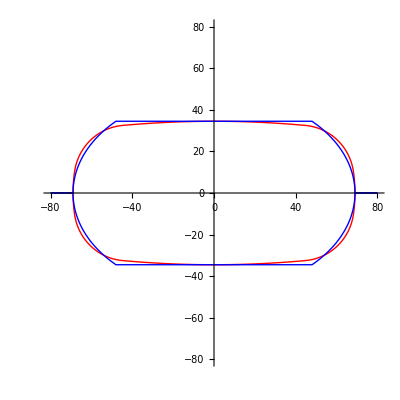

```mathematica
Show[
Plot[{g[x],-g[x]},{x,-70,70},PlotRange->{{-80,80},{-80,80}},AspectRatio->Automatic,PlotStyle->{{RGBColor[1,0,0]},{RGBColor[1,0,0]},{RGBColor[0,0,1]},{RGBColor[0,0,1]}}],
ParametricPlot[{Rectellipse[x,APER1,APER2,APER3,APER4,TILT],-Rectellipse[x,APER1,APER2,APER3,APER4,TILT]},{x,-80,80},PlotRange->{{-80,80},{-50,50}},PlotPoints->600,PlotStyle->{{RGBColor[0,0,1]},{RGBColor[0,0,1]}},AspectRatio->Automatic]
]
```

# Inner aperture.131.6mm X 62.6mm

```mathematica
Clear[x,x1,x2,y1,y2,y3,x26,y26,y500,g,r26,r69,r500,hor,ver];
r26=26-3.2;r69=69-3.2;r500=500-3.2;hor=69-3.2;ver=34.5-3.2;
y1[x_]:=Sqrt[r69^2-x^2] ;
y2[x_]:=Sqrt[r26^2-(x-x26)^2]+y26;
y500=-r500+ver;
y3[x_]:=Sqrt[r500^2-x^2]+y500;
sol=FindRoot[{  y1[x1]==y2[x1],D[y1[x1],x1]==D[y2[x1],x1],    y2[x2]==y3[x2],D[y2[x2],x2]==D[y3[x2],x2]   }, {{x1,40},{x2,50},{x26,50},{y26,10}}]
x1=sol[[1,2]]
x2=sol[[2,2]]
x26= sol[[3,2]]
y26= sol[[4,2]]
g[x_]:=0 /; x>69 ;
g[x_]:=Sqrt[r69^2-x^2] /;x ≥ x1 && x ≤69 ;
g[x_]:=Sqrt[r26^2-(x-x26)^2]+y26 /;  x≥x2  && x≤ x1 ;
g[x_]:=Sqrt[r500^2-x^2]+y500 /; x≥ 0 && x ≤ x2 ;
g[x_]:=g[-x] /; x < 0 ;
?g
```

{x1→65.0223,x2→44.5357,x26→42.4918,y26→6.59157}

65.0223

44.5357

42.4918

6.59157

Global`g

g[x_]:=0/;x>69
 
g[x_]:=√(r69^2-x^2)/;x≥x1&&x≤69
 
g[x_]:=√(r26^2-(x-x26)^2)+y26/;x≥x2&&x≤x1
 
g[x_]:=√(r500^2-x^2)+y500/;x≥0&&x≤x2
 
g[x_]:=g[-x]/;x<0

```mathematica
Clear[APER1,APER2,APER3,APER4,TILT]
```

```mathematica
APER1=hor;APER2=ver;APER3=hor;APER4=48;TILT=0;
```

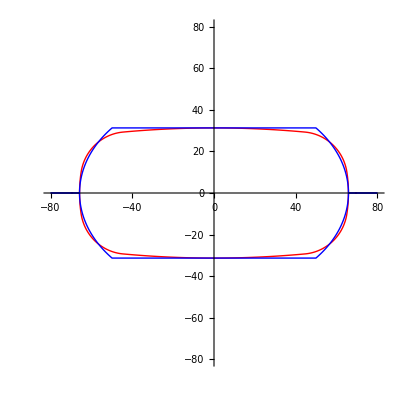

```mathematica
Show[
Plot[{g[x],-g[x]},{x,-70,70},PlotRange->{{-80,80},{-80,80}},AspectRatio->Automatic,PlotStyle->{{RGBColor[1,0,0]},{RGBColor[1,0,0]},{RGBColor[0,0,1]},{RGBColor[0,0,1]}}],
ParametricPlot[{Rectellipse[x,APER1,APER2,APER3,APER4,TILT],-Rectellipse[x,APER1,APER2,APER3,APER4,TILT]},{x,-80,80},PlotRange->{{-80,80},{-50,50}},PlotPoints->600,PlotStyle->{{RGBColor[0,0,1]},{RGBColor[0,0,1]}},AspectRatio->Automatic]
]
```

# Inner aperture with tolerances.130.7mm X 61.8mm

```mathematica
Clear[x,x1,x2,y1,y2,y3,x26,y26,y500,g,r26,r69,r500,hor,ver];
r26=26-3.2;r69=69-3.2-0.45;r500=500-3.2;hor=69-3.2-0.45;ver=34.5-3.2-0.4;
y1[x_]:=Sqrt[r69^2-x^2] ;
y2[x_]:=Sqrt[r26^2-(x-x26)^2]+y26;
y500=-r500+ver;
y3[x_]:=Sqrt[r500^2-x^2]+y500;
sol=FindRoot[{  y1[x1]==y2[x1],D[y1[x1],x1]==D[y2[x1],x1],    y2[x2]==y3[x2],D[y2[x2],x2]==D[y3[x2],x2]   }, {{x1,40},{x2,50},{x26,50},{y26,10}}]
x1=sol[[1,2]]
x2=sol[[2,2]]
x26= sol[[3,2]]
y26= sol[[4,2]]
g[x_]:=0 /; x>69 ;
g[x_]:=Sqrt[r69^2-x^2] /;x ≥ x1 && x ≤69 ;
g[x_]:=Sqrt[r26^2-(x-x26)^2]+y26 /;  x≥x2  && x≤ x1 ;
g[x_]:=Sqrt[r500^2-x^2]+y500 /; x≥ 0 && x ≤ x2 ;
g[x_]:=g[-x] /; x < 0 ;
?g
```

{x1→64.6463,x2→44.1165,x26→42.0918,y26→6.2274}

64.6463

44.1165

42.0918

6.2274

Global`g

g[x_]:=0/;x>69
 
g[x_]:=√(r69^2-x^2)/;x≥x1&&x≤69
 
g[x_]:=√(r26^2-(x-x26)^2)+y26/;x≥x2&&x≤x1
 
g[x_]:=√(r500^2-x^2)+y500/;x≥0&&x≤x2
 
g[x_]:=g[-x]/;x<0

```mathematica
Clear[APER1,APER2,APER3,APER4,TILT]
```

```mathematica
APER1=hor;APER2=ver;APER3=hor;APER4=48;TILT=0;
```

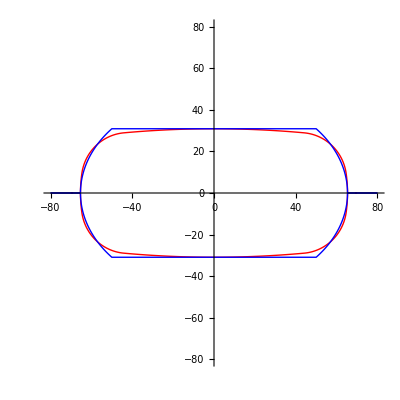

```mathematica
Show[
Plot[{g[x],-g[x]},{x,-70,70},PlotRange->{{-80,80},{-80,80}},AspectRatio->Automatic,PlotStyle->{{RGBColor[1,0,0]},{RGBColor[1,0,0]},{RGBColor[0,0,1]},{RGBColor[0,0,1]}}],
ParametricPlot[{Rectellipse[x,APER1,APER2,APER3,APER4,TILT],-Rectellipse[x,APER1,APER2,APER3,APER4,TILT]},{x,-80,80},PlotRange->{{-80,80},{-50,50}},PlotPoints->600,PlotStyle->{{RGBColor[0,0,1]},{RGBColor[0,0,1]}},AspectRatio->Automatic]
]
```

# PSB- Quadrupole magnet for QF - BETX=BETY & Ex=Ey

```mathematica
Hyperlink["\\\\cern.ch\\dfs\\Departments\\TS\\Services\\Old Drawings\\Complexe_PS\\BOOSTER\\49\\PS-SI-3-49-1063.TIF"]
```

```mathematica
Import["\\\\cern.ch\\dfs\\Departments\\TS\\Services\\Old Drawings\\Complexe_PS\\BOOSTER\\49\\PS-SI-3-49-1063.TIF"]
```

-Graphics-

# Outer apperture. r=58 mm

```mathematica
Clear[x,g,h,Ls,Lx,Ly,xoff,yoff,radiusx,radiusy,angle,x1,x2];
Ls=118;
Lx=138;
Ly=124;
radiusy=50;
radiusx=40;
yoff=(Ly-2*radiusy)/2(*12*);
xoff=(Lx-2*radiusx)/2 (*29*);
angle =-(98/2)*π/180.;


g[x_]:=Sqrt[radiusy^2-x^2]+yoff  /; x ≥ 0 && x ≤26.414463147400728 ;
g[x_]:=(Cos[angle]/Sin[angle])*x+ Ls*Cos[angle] /; x>26.414463147400728 && x≤ 60.05748171990252;
g[x_]:=Sqrt[radiusx^2-(x-xoff)^2] /; x≥ 60.05748171990252 && x ≤ Lx/2;
g[x_]:=0 /; x>Lx/2;
g[x_]:=g[-x] /; x<0;
```

```mathematica
FindMinimum[{((Sqrt[radiusy^2-x1^2]+yoff)  - ((Cos[angle]/Sin[angle])*x1+ Ls*Cos[angle]))^2,x1>0},{x1, xoff}]
```

{1.36039×10^-17,{x1→26.4145}}

```mathematica
FindMinimum[{(Sqrt[radiusx^2-(x2-xoff)^2]   - ((Cos[angle]/Sin[angle])*x2+ Ls*Cos[angle]))^2,x2>0},{x2, xoff+radiusx-1}]
```

{8.76094×10^-16,{x2→60.0575}}

```mathematica
r=58;
h[x_]:=Sqrt[r^2-x^2] /; x≥-r && x≤r;
h[x_]:=0 /; x< -r;
h[x_]:=0 /; x>r;
```

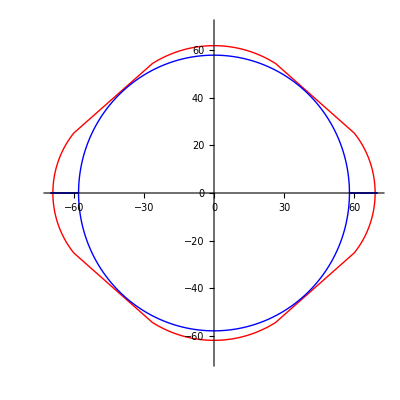

```mathematica
Plot[{g[x],-g[x],h[x],-h[x]},{x,-70,70},PlotRange->{{-70,70},{-70,70}},AspectRatio->Automatic, PlotPoints->600,PlotStyle->{{RGBColor[1,0,0]},{RGBColor[1,0,0]},{RGBColor[0,0,1]},{RGBColor[0,0,1]}}]
```

# Inner apperture. r=57 mm

```mathematica
Clear[x,g,h,Ls,Lx,Ly,xoff,yoff,radiusx,radiusy,angle,x1,x2];
Ls=118-1.5*2;
Lx=138-1.5*2;
Ly=124-1.5*2;
radiusy=50-1.5;
radiusx=40-1.5;
yoff=(Ly-2*radiusy)/2(*12*);
xoff=(Lx-2*radiusx)/2 (*29*);
angle =-(98/2)*π/180.;


g[x_]:=Sqrt[radiusy^2-x^2]+yoff  /; x ≥ 0 && x ≤25.59888288409237 ;
g[x_]:=(Cos[angle]/Sin[angle])*x+ Ls*Cos[angle] /; x>25.59888288409237&& x≤ 58.921555777604624;
g[x_]:=Sqrt[radiusx^2-(x-xoff)^2] /; x≥ 58.921555777604624 && x ≤ Lx/2;
g[x_]:=0 /; x>Lx/2;
g[x_]:=g[-x] /; x<0;
```

```mathematica
FindMinimum[{((Sqrt[radiusy^2-x1^2]+yoff)  - ((Cos[angle]/Sin[angle])*x1+ Ls*Cos[angle]))^2,x1>0},{x1, xoff}]
```

{2.60873×10^-16,{x1→25.5989}}

```mathematica
FindMinimum[{(Sqrt[radiusx^2-(x2-xoff)^2]   - ((Cos[angle]/Sin[angle])*x2+ Ls*Cos[angle]))^2,x2>0},{x2, xoff+radiusx-1}]
```

{1.50582×10^-16,{x2→58.9216}}

```mathematica
r=57;
h[x_]:=Sqrt[r^2-x^2] /; x≥-r && x≤r;
h[x_]:=0 /; x< -r;
h[x_]:=0 /; x>r;
```

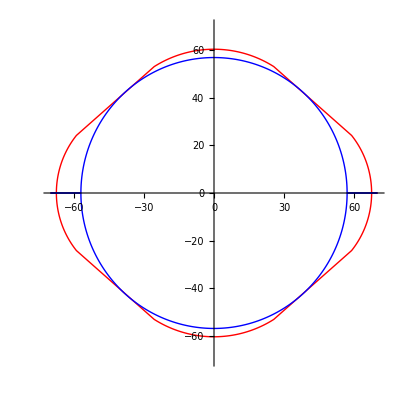

```mathematica
Plot[{g[x],-g[x],h[x],-h[x]},{x,-70,70},PlotRange->{{-70,70},{-70,70}},AspectRatio->Automatic, PlotPoints->600,PlotStyle->{{RGBColor[1,0,0]},{RGBColor[1,0,0]},{RGBColor[0,0,1]},{RGBColor[0,0,1]}}]
```

# Inner apperture with tolerance. r=57 mm

```mathematica
Clear[x,g,h,Ls,Lx,Ly,xoff,yoff,radiusx,radiusy,angle,x1,x2];
Ls=118-1.5*2;
Lx=138-1.5*2-0.3;
Ly=124-1.5*2-0.3;
radiusy=50-1.5;
radiusx=40-1.5;
yoff=(Ly-2*radiusy)/2(*12*);
xoff=(Lx-2*radiusx)/2 (*29*);
angle =-(98/2)*π/180.;


g[x_]:=Sqrt[radiusy^2-x^2]+yoff  /; x ≥ 0 && x ≤26.23148040599387 ;
g[x_]:=(Cos[angle]/Sin[angle])*x+ Ls*Cos[angle] /; x>26.23148040599387&& x≤ 58.395257373954465;
g[x_]:=Sqrt[radiusx^2-(x-xoff)^2] /; x≥ 58.395257373954465 && x ≤ Lx/2;
g[x_]:=0 /; x>Lx/2;
g[x_]:=g[-x] /; x<0;
```

```mathematica
FindMinimum[{((Sqrt[radiusy^2-x1^2]+yoff)  - ((Cos[angle]/Sin[angle])*x1+ Ls*Cos[angle]))^2,x1>0},{x1, xoff}]
```

{8.66736×10^-18,{x1→26.2315}}

```mathematica
FindMinimum[{(Sqrt[radiusx^2-(x2-xoff)^2]   - ((Cos[angle]/Sin[angle])*x2+ Ls*Cos[angle]))^2,x2>0},{x2, xoff+radiusx-1}]
```

{3.74612×10^-14,{x2→58.3953}}

```mathematica
r=57;
h[x_]:=Sqrt[r^2-x^2] /; x≥-r && x≤r;
h[x_]:=0 /; x< -r;
h[x_]:=0 /; x>r;
```

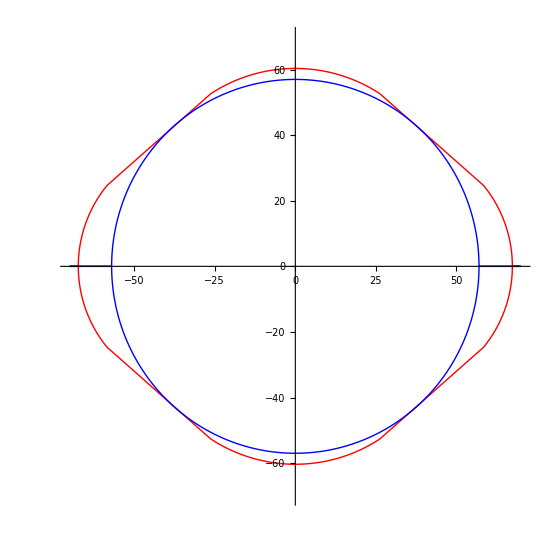

```mathematica
Plot[{g[x],-g[x],h[x],-h[x]},{x,-70,70},PlotRange->{{-70,70},{-70,70}},AspectRatio->Automatic, PlotPoints->600,PlotStyle->{{RGBColor[1,0,0]},{RGBColor[1,0,0]},{RGBColor[0,0,1]},{RGBColor[0,0,1]}}]
```

# RECTELLIPSE - KSWP1L1

```mathematica
Clear[x,APER1,APER2,APER3,APER4,TILT]
```

```mathematica
APER1=115/2;APER2=80/2;APER3=115/2;APER4=160/2;TILT=0;
```

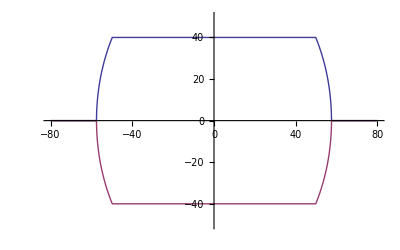

```mathematica
ParametricPlot[{Rectellipse[x,APER1,APER2,APER3,APER4,TILT],-Rectellipse[x,APER1,APER2,APER3,APER4,TILT]},{x,-80,80},PlotRange->{{-80,80},{-50,50}},AspectRatio->Automatic]
```